Создать таблицу значений функции f(x), разбив отрезок [0; 6]
на n частей неравноотстоящими точками x_i вида (a + b)/2+(b - a)/2*t_i, где t_i – корни многочлена Чебышёва T_(n+1)(t) (i = OverBar[0,n]). Для полученной таблично заданной функции f(x), выполнить следующие действия при n = 6 и n = 10:
а) создать таблицу разделенных разностей функции f(x) по точкам
(x_i, f(x_i)), i = OverBar[0,n];
б) построить интерполяционный многочлен Ньютона Pnr_n(x) для
неравноотстоящих узлов, проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и Pnr_n(x) на одном чертеже);
в) построить интерполирующую функцию Intf_n(x) с помощью функции Interpolation пакета Mathematica, проиллюстрировать графически;
г) вычислить значения функции f(x) и построенных интерполяционных
многочленов Pnr[n](x) и Intf_n(x) в точке x = 2,4316;
д) найти максимумы абсолютных погрешностей интерполирования
функции f(x) многочленом Ньютона Pnr_n(x) и функцией Intf_n(x) на
отрезке [0; 6] с помощью функции FindMaximum пакета Mathematica.
Функция f(x):

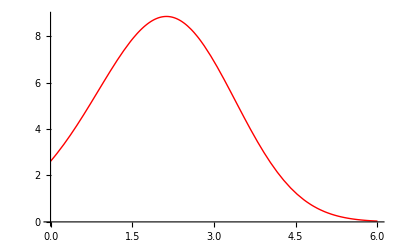

{0.0752163 | 2.82487
0.654506 | 4.79446
1.69835 | 8.3756
3. | 6.91907
4.30165 | 1.73311
5.34549 | 0.210705
5.92478 | 0.0429585,0.0305357 | 2.69765
0.271104 | 3.42906
0.732751 | 5.09374
1.37808 | 7.49762
2.1548 | 8.85275
3. | 6.91907
3.8452 | 3.26795
4.62192 | 1.00307
5.26725 | 0.255078
5.7289 | 0.0761712
5.96946 | 0.0375059}

```mathematica
f[x_]= (x + √(π+1))* Exp[-4/39*√(x^5)+5*x/9+1/4];
a = 0; b = 6; n1=6;
x0=2.4316;
n2 = 10;
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
(*Создадим таблицы значений функции для не равноотстоящих узлов на промежутке для n1=6 и n2=10. Многочлен Чебышёва для n1 и n2:*)
T1[i_]:=Cos[(π *(2 i+1))/(2*n1+2)];
T2[i_]:=Cos[(π * (2 i+1))/(2 * n2+2)];
(*Так как значения корней уменьшаются с увеличением i,полученные таблицы значений функции перевернём с помощью функции Reverse:*)
data1=Table[{x1=(a+b)/2+(b-a)/2*T1[i],f[x1]},{i,0,n1}]//N//Reverse;
data2=Table[{x2=(a+b)/2+(b-a)/2*T2[i],f[x2]},{i,0,n2}]//N//Reverse;
{TableForm[data1],TableForm[data2]}
```

a) Представим таблицу разделённых разностей функции f(x) в виде матрицы, каждый столбец которой соответствует конечным разделённым разностям соответствующего порядка от 0 до n -1 (разделённые разности 0-го порядка - значения функции в точках  x_i).
Для n=6:

```mathematica
diftab1=Array[dif1,{n1+1,n1+1},{0,0}];
(*Поскольку с увеличением порядка разделённых разностей их количество уменьшается,заполним пустые клетки таблицы:*)
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=""]];
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]];
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++, dif1[i,k]=(dif1[i+1,k-1]-dif1[i,k-1])/(data1[[i+1+k,1]]-data1[[i+1,1]])]];
PaddedForm[TableForm[diftab1],{n1,n1-1}]
```

2.82487 |  3.40001 |  0.01893 | -0.66969 |  0.21289 | -0.02555 | -0.00369
 4.79446 |  3.43073 | -1.93977 |  0.23009 |  0.07822 | -0.04712 | 
 8.37560 | -1.11898 | -1.10059 |  0.59702 | -0.17011 |  | 
 6.91907 | -3.98415 |  1.07683 | -0.12195 |  |  | 
 1.73311 | -1.45846 |  0.72014 |  |  |  | 
 0.21070 | -0.28957 |  |  |  |  | 
 0.04296 |  |  |  |  |  |

Аналогичным образом заполним таблицу для n = 10 :

```mathematica
diftab2=Array[dif2,{n2+1,n2+1},{0,0}];
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]];
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]];
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=(dif2[i+1,k-1]-dif2[i,k-1])/(data2[[i+1+k,1]]-data2[[i+1,1]])]];
PaddedForm[TableForm[diftab2//N],{n2,n2-1}]
```

2.697649620 |  3.040356382 |  0.805438517 | -0.517861329 | -0.131132839 |  0.082917095 | -0.006544356 | -0.004362921 |  0.001652871 | -0.000253693 | -7.454649238×10^-6
 3.429063106 |  3.605947876 |  0.107598692 | -0.796422446 |  0.115086517 |  0.057952588 | -0.026576213 |  0.004292689 |  0.000207235 | -0.000297966 | 
 5.093739073 |  3.725056780 | -1.392620928 | -0.482363312 |  0.322214495 | -0.057675690 | -0.005129320 |  0.005423732 | -0.001490683 |  | 
 7.497616074 |  1.744678724 | -2.486258530 |  0.520512030 |  0.097903863 | -0.080934579 |  0.021968428 | -0.002382547 |  |  | 
 8.852751275 | -2.287839809 | -1.202092826 |  0.838096979 | -0.216864570 |  0.014646064 |  0.011029235 |  |  |  | 
 6.919074398 | -4.319851922 |  0.865593094 |  0.163117631 | -0.164518164 |  0.056718868 |  |  |  |  | 
 3.267945617 | -2.915927047 |  1.235421335 | -0.285835326 |  0.003906491 |  |  |  |  |  | 
 1.003072817 | -1.159094838 |  0.696993814 | -0.277536898 |  |  |  |  |  |  | 
 0.255078468 | -0.387541133 |  0.323001222 |  |  |  |  |  |  |  | 
 0.076171165 | -0.160724635 |  |  |  |  |  |  |  |  | 
 0.037505906 |  |  |  |  |  |  |  |  |  |

б) Построим интерполяционные многочлены Ньютона для не равноотстоящих узлов при n1 = 6 и n2 = 10.
Введём вспомогательные многочлены P(x) и построим интерполяционные многочлены с их помощью:

```mathematica
P1[x_]=1;P2[x_]=1;Pnr1[x_]=dif1[0,0];Pnr2[x_]=dif2[0,0];
For[i=0,i<n1,i++,P1[x_]=P1[x] (x-data1[[i+1,1]]);Pnr1[x_]=Pnr1[x]+dif1[0,i+1] P1[x]]
Pnr1[x]//Simplify
```

2.68576+1.58569 x+3.64519 x^2-1.8614 x^3+0.152087 x^4+0.0300246 x^5-0.00368673 x^6

```mathematica
For[i=0,i<n2,i++,P2[x_]=P2[x] (x-data2[[i+1,1]]);Pnr2[x_]=Pnr2[x]+dif2[0,i+1] P2[x]]
Pnr2[x]//Simplify
```

2.61524+2.65132 x+1.60146 x^2-1.47419 x^3+1.51446 x^4-1.10096 x^5+0.379121 x^6-0.063787 x^7+0.00475427 x^8-0.0000521902 x^9-7.45465×10^-6 x^10

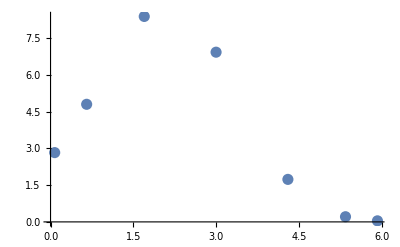

```mathematica
(*Изобразим полученные интерполяционные многочлены.*)
graph1D=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}]
```

```mathematica
(*Интерполяционный многочлен Ньютона для не равноотстоящих узлов при n=6:*)
```

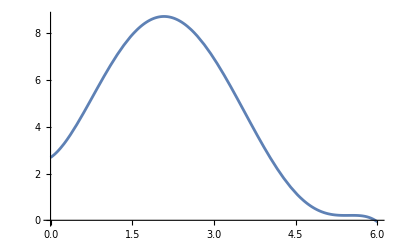

```mathematica
graph1Pnr=Plot[Pnr1[x],{x,a,b}]
```

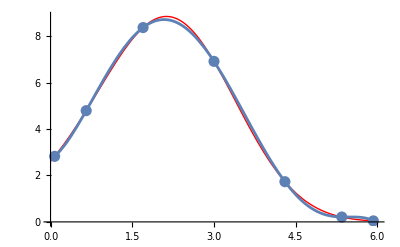

```mathematica
Show[graph,graph1D,graph1Pnr]
```

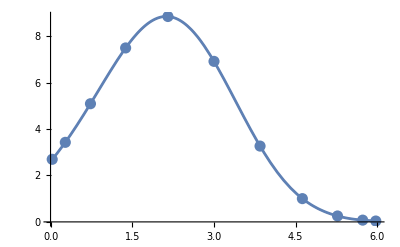

```mathematica
(*Интерполяционный многочлен Ньютона для не равноотстоящих узлов при n=10:*)
graph2Pnr=Plot[Pnr2[x],{x,a,b}];
graph2D=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}];
Show[graph,graph2D,graph2Pnr]
```

в) Интерполирующие функции функции f(x) при n1 = 6 и n2 = 10, построенные встроенной функцией пакета Mathematica:

```mathematica
Intf1=Interpolation[data1]
```

InterpolatingFunction[…]

```mathematica
Intf2=Interpolation[data2]
```

InterpolatingFunction[…]

```mathematica
(*Изобразим полученные интерполирующие функции.
Интерполирующая функция при n=6:*)
```

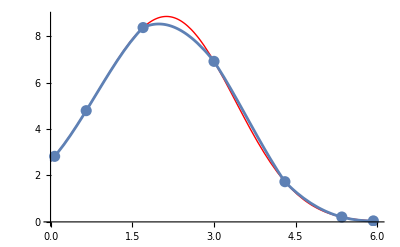

```mathematica
graph1Intf=Plot[Intf1[x],{x,a,b}];
Show[graph,graph1D,graph1Intf]
```

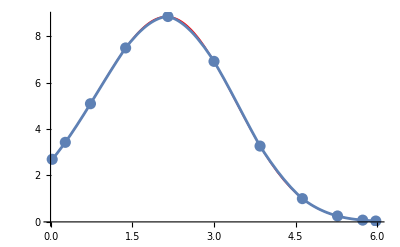

```mathematica
(*Интерполирующая функция при n=10:*)
graph2Intf=Plot[Intf2[x],{x,a,b}];
Show[graph,graph2D,graph2Intf]
```

г) Значения интерполяционных многочленов Ньютона для не равноотстоящих узлов в точке x0:

```mathematica
Print["f[x]=",f[x0]]
```

f[x]=8.60116

```mathematica
Print["Pnr1[x0]=",Pnr1[x0],", Pnr2[x0]=",Pnr2[x0]]
```

Pnr1[x0]=8.43968, Pnr2[x0]=8.59789

```mathematica
(*Значения интерполирующих функций в точке x0:*)
Print["Intf1[x0]=",Intf1[x0],", Intf2[x0]=",Intf2[x0]]
```

Intf1[x0]=8.19314, Intf2[x0]=8.52437

д) Исследуем погрешность интерполяционного многочлена Ньютона для неравноотстоящих узлов и интерполирующей функции при n = 6.

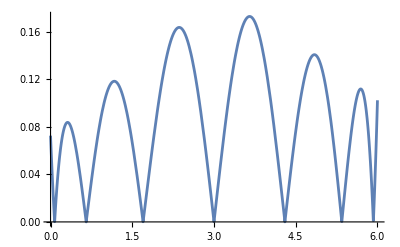

```mathematica
Rnp1[x_]=Abs[f[x]-Pnr1[x]]//Simplify;
(*График погрешности Rnp1(x):*)
graphErrp1=Plot[Rnp1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrp1=FindMaximum[{Rnp1[x],0<=x<=6},x]
```

{0.0838514,{x→0.31325}}

```mathematica
(*Результат не соответствует графику, надо уточнить*)
```

```mathematica
maxErrp1=FindMaximum[{Rnp1[x],3<=x<=6},x]
```

{0.1731,{x→3.65346}}

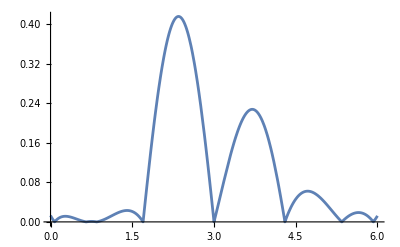

```mathematica
RnI1[x_]=Abs[f[x]-Intf1[x]]//Simplify;
(*График погрешности RnI1(x):*)
graphErrI1=Plot[RnI1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI1=FindMaximum[RnI1[x],{x,1,3}]
```

{0.415942,{x→2.34888}}

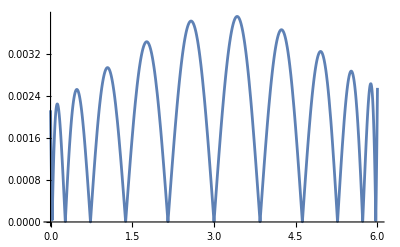

```mathematica
(*Аналогимчным образом исследуем погрешность интерполяционного многочлена Ньютона для неравноотстоящих узлов и интерполирующей функции при n=10.*)
Rnp2[x_]=Abs[f[x]-Pnr2[x]]//Simplify;
(*График погрешности Rnp2(x):*)
graphErrp2=Plot[Rnp2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrp2=FindMaximum[Rnp2[x],{x,3,5}]
```

{0.00391923,{x→3.42477}}

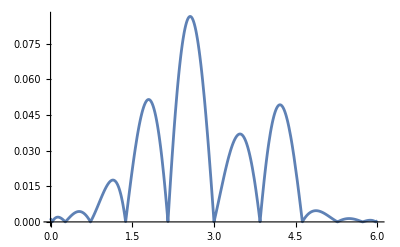

```mathematica
RnI2[x_]=Abs[f[x]-Intf2[x]]//Simplify;
(*График погрешности RnI2(x):*)
graphErrI2=Plot[RnI2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI2=FindMaximum[RnI2[x],{x,2.5,4}]
```

{0.0864096,{x→2.5628}}

Для равностоящих :
 1) maxErr1:  {0.366789, {x → 5.6539}}
 2)maxErr2: {0.0310142, {x → 5.82281}}
 
  Для неравностоящих :
 1) maxErr1: {0.415942, {x → 2.34888}}
 2)maxErr2: {0.00391923, {x → 3.42477}}
 
  Из сравнения результатов вычисления максимальных погрешностей можно сделать вывод о том, что с увеличением количества узлов интерполяции возрастает точность построения интерполяционных многочленов (в обоих случаях значение погрешности при n2 = 10 значительно меньше значения при n1 = 6).
  Неравностоящие узлы демонстрируют более низкие максимальные погрешности, что позволяет сделать вывод о преимуществах использования адаптивных методов интерполяции.